A Gaussian with a width α and center shifted by β is defined as:
g_α( x ; α, β ) = ⅇ^(-α ( x - β )^2)

The coefficients of a Fourier series of g_α for the interval L=(b - a) is given as:
f_n = (∫_a)^b dx g_α( x; α, β ) ⅇ^(-2π n ⅈ x / L) 
where -∞<n<∞.

The Fourier transform of  g_αis
f̃(k) = (∫_(-∞))^∞dx ⅇ^(-ⅈ k x)g_α( x; α, β ) = ⅇ^(-ⅈ k β)√(π/α)ⅇ^(-k^2/(4 α))

```mathematica
Clear["Global`*"]
```

```mathematica
b = 50;
a = -b;
L = b - a;
α= 1/25;
β = 20;
```

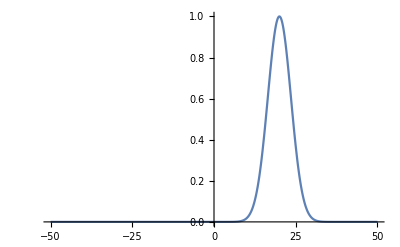

```mathematica
Plot[ⅇ^(-α ( x - β )^2),{x,a,b}, PlotRange->All]
```

```mathematica
fn[n_]:=Integrate[ⅇ^(-α*(x - β)^2) ⅇ^((-2*π*n)/L*ⅈ*x),{x,a,b}]
```

```mathematica
N[fn[0]]
```

8.86227

```mathematica
N[fn[{0, 1, 2, 3}]]
```

{8.86227,2.67185-8.2231 ⅈ,-6.4959-4.71955 ⅈ,-5.74196+4.17178 ⅈ}

```mathematica
k[n_]:=(2*π*n)/L
```

```mathematica
f[k_]:=ⅇ^(-ⅈ*k*β)√(π/α)ⅇ^(-k^2/(4 α))
```

```mathematica
N[f[k[{0, 1, 2, 3}]]]
```

{1.77245,1.68404-0.547178 ⅈ,1.4283-1.03772 ⅈ,1.03261-1.42126 ⅈ}

```mathematica
fdif[n_]:=fn[n]-f[k[n]]
```

```mathematica
N[fdif[{0, 1, 2, 3}]]
```

General::munfl: Exp[-3029.01+3.45632 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2028.81-2.82813 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3029.+6.91265 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.,0.-2.22045×10^-16 ⅈ,0.+0. ⅈ,-4.44089×10^-16+0. ⅈ}

```mathematica
Norm[N[fdif[Range[-100, 100]]]]
```

3.00656×10^-15